### Wprowadzenie wartosci dla czasu ruchu rakiety ( "t" ), szybkosci spalania paliwa ( "μ" ) i przyspieszenia ziemskiego ( "g" ).

```mathematica
ClearAll["Global`*"];
```

```mathematica
t=5;             (* s *)
```

```mathematica
μ=0.1;       (* kg/s *)
```

```mathematica
g=9.81;     (* m/s^2 *)
```

### Wprowadzenie wzorow na mase spalin wyrzuconych w czasie "t" ( "m_s" ), sile grawitacji dzialajaca na rakiete podczas ruchu ( "F_g" ) i sile ciagu rakiety ( "F_c" ). Symbole "m" i "v" oznaczaja odpowiednio mase poczatkowa rakiety i szybkosc wylatujacych spalin.

```mathematica
ms=μ×t;
Fg=(m-ms)×g;
Fc=μ×v;
```

Null^3

### Zastosowanie drugiej zasady dynamiki do obliczenia przyspieszenia rakiety ( "a" ) dla czasu trwania ruchu t = 5 s.

```mathematica
A=Solve[ (m-ms)×a==Fc-Fg,a];
```

### Sporzadzenie wykresu obrazujacego zaleznosc przyspieszenia rakiety od szybkosci wylatujacych spalin dla poczatkowej masy rakiety rownej 1 kg.

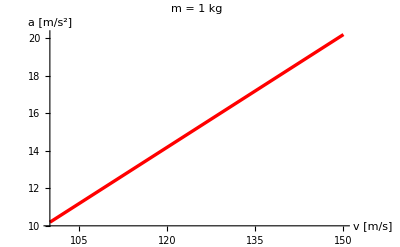

```mathematica
rys1=Plot[a/.A/.m->1,{v,100,150},TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     m = 1 kg  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v [m/s]","a [m/s^2] "}]
```

### Sporzadzenie wykresu obrazujacego zaleznosc przyspieszenia rakiety od szybkosci wylatujacych spalin dla poczatkowej masy rakiety rownej 1.5 kg.

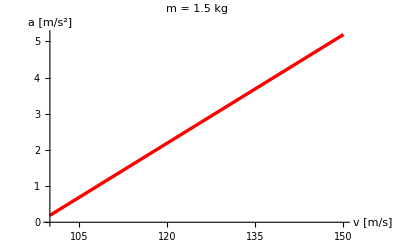

```mathematica
rys1=Plot[a/.A/.m->1.5,{v,100,150},TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     m = 1.5 kg  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v [m/s]","a [m/s^2] "}]
```